# 数学建模

导入数据

```mathematica
data=Import["G:\\GitHub Local Repository\\Mathematical-Modeling-Campus-Competition\\2020年兰州大学数学建模竞赛赛题 (1)\\Data.xlsx"];
```

```mathematica
data//Dimensions
```

{2}

```mathematica
train=data[[1,2;;All]];
```

```mathematica
test=data[[2,2;;All]];
```

数据预处理

```mathematica
asso=MapThread[Rule,{train[[All,1;;7]],train[[All,8]]}][[2;;All]];
```

```mathematica
model=Classify[asso,Method->"SupportVectorMachine"];
```

## 探索 7指标分类器

```mathematica
Information[model]
```

Classifier information
Data type | NumericalVector (length: 7)
Classes | ,,0.1.
Accuracy | (91.80.8) %
Method | SupportVectorMachine
Single evaluation time | 6.66 ms/example
Batch evaluation speed | 5.12 examples/ms
Loss | 0.257 ± 0.014
Model memory | 1.21 MB
Training examples used | 19999 examples
Training time | 1 32
 |

```mathematica
model[test[[2]]]
```

1.

## 进行主成分分析

```mathematica
features=train[[All,1;;7]];
```

```mathematica
lables=train[[All,8]];
```

得到降维后的数据

```mathematica
reduced=(KarhunenLoeveDecomposition[Transpose[features]][[1]]//Transpose)[[All,1;;2]];
```

现在要求出主向量

```mathematica
{b,m}=KarhunenLoeveDecomposition[Transpose[features],Standardized->False];
```

对降维后的数据进行画图操作：

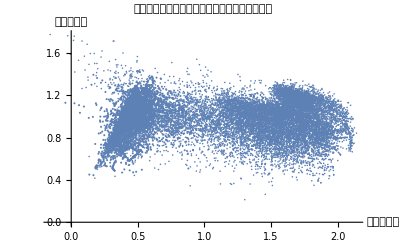

```mathematica
Show[ListPlot@point1,ListPlot@point2,AxesLabel->{"第一主成分","第二主成分"},PlotLabel->"训练集在两个最主成分构成的特征空间中的分布"]
```

```mathematica
path="G:\\GitHub Local Repository\\Mathematical-Modeling-Campus-Competition";
```

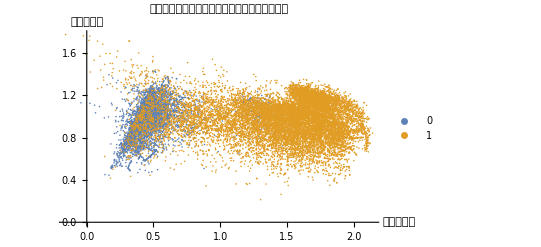
```mathematica
Export[path<>"\\训练集在两个最主成分构成的特征空间中的分布图（有色）.jpg",-Graphics-];
```

```mathematica
po1=Position[lables,x_/;x==1]//Flatten;
```

```mathematica
po2=Position[lables,x_/;x==0]//Flatten;
```

```mathematica
point1=reduced[[po1]];
```

```mathematica
point2=reduced[[po2]];
```

```mathematica
point1//Dimensions
```

{13895,2}

```mathematica
ListPlot[{point2,point1},PlotRange->{Full,All},AxesLabel->{"第一主成分","第二主成分"},PlotLabel->"训练集在两个最主成分构成的特征空间中的分布",PlotLegends->{0,1}]
```

-Graphics-

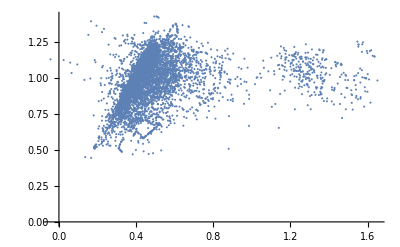

```mathematica
ListPlot[{point2},PlotRange->{Full,All}]
```

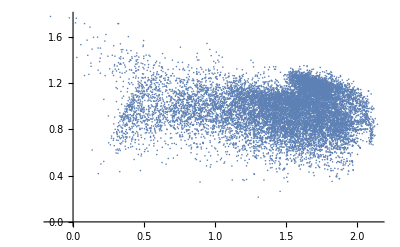

```mathematica
ListPlot[{point1},PlotRange->{Full,All}]
```

我们来探究一下主成分分析的合理性，首先我们求取协方差矩阵。

```mathematica
Covariance[features]//MatrixForm//TeXForm
```

\left(
\begin{array}{ccccccc}
 0.0985186 & 0.0943964 & 0.0853236 & 0.0304429 & 0.0527863 & 0.0124883 & 0.014629 \\
 0.0943964 & 0.109691 & 0.0843306 & 0.0344634 & 0.0559192 & 0.0162319 & 0.0191176 \\
 0.0853236 & 0.0843306 & 0.0849893 & 0.0273838 & 0.0516196 & 0.0112965 & 0.0144296 \\
 0.0304429 & 0.0344634 & 0.0273838 & 0.0172714 & 0.0219271 & 0.0109203 & 0.00977298 \\
 0.0527863 & 0.0559192 & 0.0516196 & 0.0219271 & 0.0443377 & 0.0141748 & 0.017051 \\
 0.0124883 & 0.0162319 & 0.0112965 & 0.0109203 & 0.0141748 & 0.015963 & 0.011729 \\
 0.014629 & 0.0191176 & 0.0144296 & 0.00977298 & 0.017051 & 0.011729 & 0.0153588 \\
\end{array}
\right)

```mathematica
eig=Covariance[features]//Eigenvalues;
```

```mathematica
eig/Total[eig]//TeXForm
```

\{0.840721,0.0756435,0.0358832,0.018512,0.0117046,0.0113928,0.00614299\}

```mathematica
Accumulate[eig]/Total[eig]//TeXForm
```

\{0.840721,0.916364,0.952248,0.97076,0.982464,0.993857,1.\}

## 定义计算

```mathematica
count[x_,y_][r_,point_]:=(If[(x-r)<#[[1]]<(x+r)&&(y-r)<#[[2]]<(y+r),1,0]&/@point//Total)
```

衬比度

```mathematica
Obvious[x_,y_]:=If[
x≠0||y≠0,Abs@(x-y)/(x+y),0.3
]//N
```

```mathematica
p[r_,h_,point_]:=ParallelTable[{x,y,count[x,y][r,point]},{x,0,2.5,h},{y,0,2,h}];
```

```mathematica
list[r_,h_]:=MapThread[{#1[[1]],#1[[2]],Obvious[#1[[3]],#2[[3]]]}&,{p[r,h,point1],p[r,h,point2]},2];
```

```mathematica
contour=Flatten[list[0.05,0.1],1];
```

```mathematica
contour//Dimensions
```

{546,3}

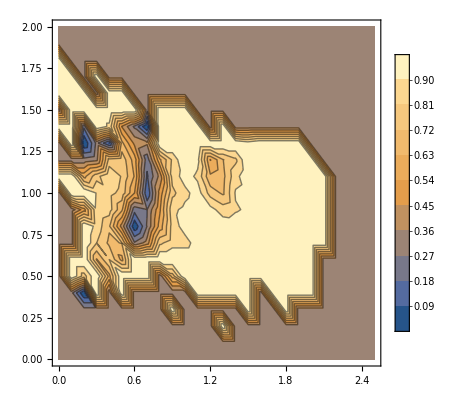

```mathematica
con=ListContourPlot[contour,PlotLegends->Automatic,Contours->10]
```

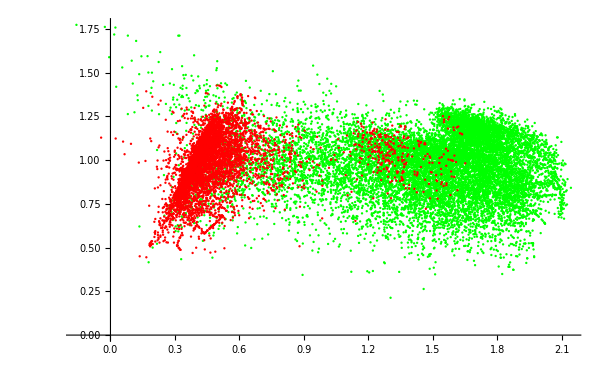

```mathematica
lis=ListPlot[{point1,point2},PlotStyle->{Green,Red}]
```

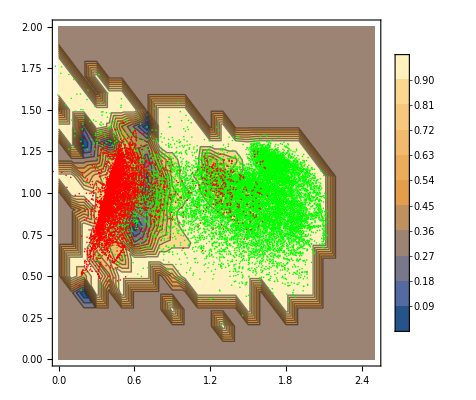

```mathematica
Show[con,lis]
```

## 对测试集进行降维

```mathematica
transformedtest=Transpose[m.Transpose[test]][[All,1;;2]];
```

```mathematica
transformedtest//Dimensions
```

{5000,2}

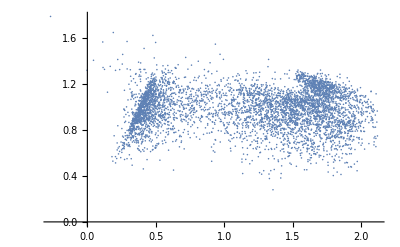

```mathematica
ListPlot[transformedtest]
```

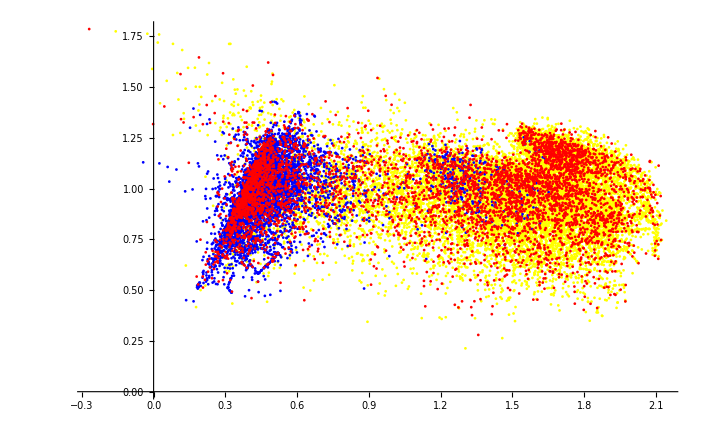

```mathematica
ListPlot[{point1,point2,transformedtest},PlotStyle->{Yellow,Blue,Red}]
```

```mathematica
asso2=MapThread[Rule,{reduced,lables}];
```

```mathematica
model2=Classify[asso2,Method->{"SupportVectorMachine","KernelType"->"Linear"}];
```

```mathematica
model2//Information
```

Classifier information
Data type | NumericalVector (length: 2)
Classes | ,,0.1.
Accuracy | (93.00.7) %
Method | SupportVectorMachine
Single evaluation time | 4.19 ms/example
Batch evaluation speed | 12.2 examples/ms
Loss | 0.244 ± 0.02
Model memory | 1. MB
Training examples used | 20000 examples
Training time | 38.1 s
 |

```mathematica
plotb=Plot3D[{
model2[{x,y},"Probability"->1.],
model2[{x,y},"Probability"->0.]
},
{x,-6,6},{y,-6,6},
 Exclusions->None]
```

-Graphics3D-

```mathematica
Show[plota,plotb,ViewPoint->Above]
```

-Graphics3D-

```mathematica
model2/@transformedtest[[1;;20]]
```

{1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.,1.,1.,0.}

```mathematica
model/@test[[1;;20]]
```

{1.,1.,1.,1.,0.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.,1.,1.,0.}